## Parameters [Always run]

```mathematica
Needs["NumericalCalculus`"]

Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

```mathematica
gcm3toMeVfm3=1.7827*10^12;
Gj=667408./100000 10^-11*(10^-3)^3* 1988/1000 10^30*(299792458/1000)^-2;
nconvSI=10^45/(19733/100)^3;econvSI=1602/1000 10^-13;
nconv=nconvSI (10^-3)^-3;
econv=econvSI (10^-3)^2(299792458/1000)^-2(1988/1000 10^30)^-1;
edconv=econv nconv;
clight=1;

nsat=0.16;
scale=197.3^3
```

7.68035×10^6

```mathematica
2*(1.32712440018*^11)*1.4/(11*(2*10^8)^2)
```

8.44534×10^-7

```mathematica
1.32712440018*10^20/1000^3
```

1.32712×10^11

```mathematica
G=6.67384*10^-8;
c=2.99792458*10^10;
Msun=1.9885469*10^33;
NaturalDensity=Msun/((G Msun)/c^2)^3;(*g/cm^3*)
NaturalLength=(G Msun)/c^2(*km*);

ChosenWorkingPrecision=21;
ChosenAccuracyGoal=18;
ChosenPrecisionGoal=18;
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jacquelynnoronhahostler/Dropbox/neutronStars/Github_version

```mathematica
MMax=2;
RadMin=13.02-1.06-1;
RadMax=13.02+1.24;
MRadMax=1.44+0.15;
MRadMin=1.44-0.15;
```

```mathematica
GW17m2={1.15,1.36};
GW17m1={1.36,1.62};
GW17R2=10.7+{-1.5,2.1};
GW17R1=10.8+{-1.7,2.};
```

### numerical derivatives needed below

```mathematica
dnum[list_]:=Module[{out},
out=Table[{(list[[i,1]]+list[[i-1,1]])/2,(list[[i,2]]-list[[i-1,2]])/(list[[i,3]]-list[[i-1,3]])},{i,2,Length[list]}];

Return[out];
] (*this calculates the speed of sound numerically *)
```

```mathematica
dchi[list_]:=Module[{out},
(*mu [fm-1], rho [fm^-3]*)
out=Table[{(list[[i,2]]+list[[i-1,2]])/(2*nsat),(list[[i,2]]-list[[i-1,2]])/(list[[i,1]]-list[[i-1,1]])/((list[[i,1]]+list[[i-1,1]])/2)^2},{i,2,Length[list]}];

Return[out];
] (*this calculates the susceptibility*)
```

```mathematica
dchi3[list_]:=Module[{out,out2},
(*mu [fm-1], rho [fm^-3]*)
out=Table[{(list[[i,1]]+list[[i-1,1]])/2,(list[[i,2]]-list[[i-1,2]])/(list[[i,1]]-list[[i-1,1]]),(list[[i,2]]+list[[i-1,2]])/2},{i,2,Length[list]}];
out2=Table[{(out[[i,3]]+out[[i-1,3]])/(2*nsat),(out[[i,2]]-out[[i-1,2]])/(out[[i,1]]-out[[i-1,1]])/((out[[i,1]]+out[[i-1,1]])/2)},{i,2,Length[out]}];

Return[out2];
] (*this calculates the susceptibility*)
```

### LIGO constraints

```mathematica
Gw1=Import["input_files/LVC_NICER/GW170817_spectralEOS_wMaxm_90confidence_R1[km]_m1[Msun].dat"];
Gw2=Import["input_files/LVC_NICER/GW170817_spectralEOS_wMaxm_90confidence_R2[km]_m2[Msun].dat"];
```

```mathematica
shade[gw1_,gw2_]:=Module[{pol1,pol2,out},

pol1=Polygon[gw1];
pol2=Polygon[gw2];
out=Show[{Plot[z/5,{z,0,2},PlotRange->{{5,15},{0,3}}],Graphics[{EdgeForm[Thick],Pink,pol1}],Graphics[{EdgeForm[Thick],Pink,pol2}]}];


Return[out];

]
```

## TOV Solver [Always run]

### Mass radius calc

```mathematica
dr=10^-7;
Rmax=10^20;
```

```mathematica
mr[p0_,en_]:=Module[{sol,f1,f2,rmax,mmax,minp},
Clear[M];
Clear[p];
minp=1.6906320566287588*10^-25;
sol=NDSolve[{p'[rr]==If[rr>dr,-(Gj*(M[rr] clight^2+4.π*rr^3 p[rr]))/(clight^4 rr^2)*(en[p[rr]] clight^2+p[rr])*(1-(2*Gj*M[rr])/(clight^2 rr))^-1,-(4π)/3. Gj/clight^4 rr*(en[p0]+p0)*(en[p0]+3p0)],M'[rr]==4π*rr^2 en[p[rr]] ,p[0]==p0,M[0]==0,WhenEvent[p[rr]≤minp,{R= rr,Mmax= M[rr],"StopIntegration"},"DetectionMethod"->"Interpolation"]},{p,M},{rr,0,20},Method->"StiffnessSwitching",WorkingPrecision->23];
f1[x_]:=M[x]/.sol[[1,2]];
f2[x_]:=p[x]/.sol[[1,1]];  
rmax=x/.FindRoot[f2[x]==0,{x,10}];
mmax=f1[rmax];


Return[{rmax,mmax,en[p0]/(scale*edconv),p0/(scale*edconv)}];

]
mre0[p0_,en_]:=Module[{sol,f1,f2,rmax,mmax},
Clear[M];
Clear[p];
sol=NDSolve[{p'[rr]==If[rr>dr,-(Gj*(M[rr] clight^2+4π*rr^3 p[rr]))/(clight^4 rr^2)*(en[p[rr]] clight^2+p[rr])*(1-(2*Gj*M[rr])/(clight^2 rr))^-1,-(4π)/3 Gj/clight^4 rr*(en[p0]+p0)*(en[p0]+3p0)],M'[rr]==4π*rr^2 en[p[rr]] ,p[0]==p0,M[0]==0,WhenEvent[p[rr]≤0,{R= rr,Mmax= M[rr],"StopIntegration"},"DetectionMethod"->"Interpolation"]},{p,M},{rr,0,20},Method->"StiffnessSwitching",WorkingPrecision->23];
f1[x_]:=M[x]/.sol[[1,2]];
f2[x_]:=p[x]/.sol[[1,1]];
rmax=x/.FindRoot[f2[x]==0,{x,10}];
mmax=f1[rmax];
Return[{rmax,mmax,en[p0]/(scale*edconv),p0/(scale*edconv)}];

]
```

If you just want to get the mass-radius relationship, you just need to run genmr[enint]

```mathematica
p0list=Join[Table[x*10^-4,{x,0.01,1,0.01}],Table[x*10^-4,{x,1.1,15,0.1}],Table[x*10^-4,{x,101,1000,20}]];
p0twn=Join[Table[x*10^-4,{x,0.01,0.5,0.01}],Table[x*10^-4,{x,0.6,15,0.1}],Table[x*10^-4,{x,101,1000,10}],Table[x*10^-4,{x,1001,10000,100}]];
Length[p0list]
```

285

```mathematica
genmr[eos_]:=Select[Join[Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.01,1,0.01}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,1.1,15,0.1}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,101,1000,20}]]],#[[2]]>0&]
```

```mathematica
genmrTW[eos_]:=Select[Join[Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.1,1,0.01}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,1.1,15,0.1}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,20,95,2.5}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,101,1000,10}]]],#[[2]]>0&]
```

```mathematica
(*genmrTW[eos_]:=Select[Join[Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,0.1,1,0.01}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,1,15,0.1}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,20,95,2.5}]],Parallelize[Table[Quiet[mr[x*10^-4,eos]],{x,101,1000,10}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,1001,10000,100}]]],#[[2]]>0&]*)
```

```mathematica
genmrMORE[eos_]:=Select[Join[Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,0.01,0.1,0.01}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,0.2,1,0.05}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,1,15,1.5}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,20,95,5}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,101,1000,20}]],Parallelize[Table[Quiet[mre0[x*10^-4,eos]],{x,1001,10000,100}]]],#[[2]]>0&]
```

```mathematica
0.000841
```

0.000841

### ConvertToEOS

#### normal EOS reconstruct

```mathematica
EOSrecon[f_,ic_,dn_]:=Module[{e0,n0,p0,n,ee,p},
n0=ic[[1]];
e0=ic[[2]];
p0=ic[[3]];

n=n0+dn;
ee=e0+dn*(e0+p0)/n0;
p=p0+f[n0]*dn*(e0+p0)/n0;

Return[{n,ee,p}];
]
ConvertInterpolate[tabMeVfm3_]:=Module[{entab,enint},
entab=Table[{edconv*scale*tabMeVfm3[[i,2]],edconv*scale*tabMeVfm3[[i,3]]},{i,Length[tabMeVfm3]}]; (* table of energy density in terms of pressure *)
enint=Interpolation[entab,InterpolationOrder->1]; (*interpolation function, too high of order causes issues *)
Return[enint];
] 
comblowden[lowdenin_,frun_,rhosat_]:=Module[{enext,pnext,nc,ni,nn,lm,tlow,entab,alltab,en,Es,Ps,lowdensub,lowden,ttsub,ep,derv,erho,prho,murho, chi2,chi3,c2,c3,tabgcm3,ϵofp,pofϵ,tabMeVfm3},
erho=Interpolation[lowdenin[[All,{1,3}]],InterpolationOrder->1];
prho=Interpolation[lowdenin[[All,{1,2}]],InterpolationOrder->1];


Es=erho[rhosat];
Ps=prho[rhosat];

lowdensub=Select[lowdenin,#[[1]]<rhosat&]; (*rho/rho0 [fm^-3], pressure [MeV/fm^-3], energy density [MeV/fm^-3] *)
lowden=edconv*scale*lowdensub[[All,{3,2}]];
enext=Es;
pnext=Ps;
(*f[0]={0,0,0};
nc[1]=0;
ni=2;*)
ni=1;
For[nn=rhosat,nn≤50,nn=nn+0.005,
f[nn]=EOSrecon[frun,{nn,enext,pnext},0.005];

enext=f[nn][[2]];
pnext=f[nn][[3]];
nc[ni]=nn;
ni++;
];
(*FORMAT {{"n [fm^-3]","p [MeV/fm^3]","e [MeV/fm^3]","cs^2","muB [MeV]"}}*)
ttsub=Join[Table[{nsat*lowdensub[[i,1]],lowdensub[[i,2]],lowdensub[[i,3]],frun[lowdensub[[i,1]]],(lowdensub[[i,2]]+lowdensub[[i,3]])/(nsat*lowdensub[[i,1]])},{i,Length[lowdensub]}],Table[{nsat*nc[i],f[nc[i]][[3]],f[nc[i]][[2]],frun[nc[i]],(f[nc[i]][[3]]+f[nc[i]][[2]])/(nsat*nc[i])},{i,ni-1}]]; (* density,  pressure, energy density, cs2, muB *)



tabgcm3=Table[{gcm3toMeVfm3*ttsub[[i,2]],gcm3toMeVfm3*ttsub[[i,3]]},{i,2,Length[ttsub]}];
(* this table must be in the format  pressure [g/cm^3], energy density [g/cm^3] to use in the I Love Q below*)
(*EoS*)



(*EoSTable="eosAPR.dat";
{ϵofp,pofϵ}=InterpolatingEoS[tabgcm3,ChosenWorkingPrecision];*)

(*ep=Interpolation[Delete[ttsub[[All,{1,2}]],1]];

(*mu [fm-1], rho [fm^-3]*)
murho=Table[{ttsub[[i,5]]/197.3,ttsub[[i,1]]},{i,2,Length[ttsub]}];
chi2=dchi[murho];
chi3=dchi3[murho];
c2=ListLinePlot[chi2,ImageSize->500,PlotStyle->MyStyle,PlotRange->{{0.001,7},{0,0.1}},FrameLabel->{Style["n/n_sat",20],Style["χ_2/μ_B^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
c3=ListLinePlot[chi3,ImageSize->500,PlotStyle->MyStyle,PlotRange->{{0.001,7},{-2,2}},FrameLabel->{Style["n/n_sat",20],Style["χ_3/μ_B",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
Print[c2];
Print[c3];


entab=Table[{edconv*scale*f[nc[i]][[2]],edconv*scale*f[nc[i]][[3]]},{i,ni-1}]; (*pressure, energy density*)
alltab=Join[lowden,entab];
en=Interpolation[alltab[[All,{2,1}]],InterpolationOrder->1];

Return[en];*)
Return[ttsub];
]
```

## Style [Always run]

```mathematica
Needs["ErrorBarPlots`"]
thick=0.008;
MyStyle={
Directive[Thickness[thick],Black],
Directive[Thickness[thick],Red],(*"2bumpsfat"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Red],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Red],
Directive[Dashing[{0.01,0.01}],Red],
Directive[Thickness[thick],Blue],(*"endpoint"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Green]],(*"2bumpsthin"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Cyan],(*"slanted"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Cyan],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Cyan],
Directive[Dashing[{0.01,0.01}],Cyan],
Directive[Thickness[thick],Magenta],(*"oscilliations"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Magenta],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Magenta],
Directive[Dashing[{0.01,0.01}],Magenta],
Directive[Thickness[thick],Orange],(*"adjustedwidth"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Orange],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Orange],
Directive[Dashing[{0.01,0.01}],Orange],
Directive[Thickness[thick],Orange],(*"peaklocation"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Orange],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Orange],
Directive[Dashing[{0.01,0.01}],Orange],
Directive[Thickness[thick],Darker[Green]],(*"endpoint_max"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Brown],(*"peaklocation_adjustwidth"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Brown],Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Brown],
Directive[Dashing[{0.01,0.01}],Brown],
Directive[Thickness[thick],Darker[Gray]],(*"afterbump"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Gray]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Gray]],
Directive[Dashing[{0.01,0.01}],Darker[Gray]],
Directive[Thickness[thick],Darker[Green]],(*"endpoint_noslant"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Pink],(*"endpoint2"*)
Directive[Thickness[thick],Dashing[{0.03,0.03}],Pink],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Pink],
Directive[Dashing[{0.01,0.01}],Pink],
Directive[Thickness[thick],Black],
Directive[Thickness[thick],Darker[Red]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Red]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Red]],
Directive[Dashing[{0.01,0.01}],Darker[Red]],
Directive[Thickness[thick],Gray],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Gray],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Gray],
Directive[Dashing[{0.01,0.01}],Gray],
Directive[Thickness[thick],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Orange]],
Directive[Dashing[{0.01,0.01}],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Purple]],
Directive[Dashing[{0.01,0.01}],Darker[Purple]],
Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Dashing[{0.01,0.01}],Darker[Yellow]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Magenta]],
Directive[Dashing[{0.01,0.01}],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Blue]],
Directive[Dashing[{0.01,0.01}],Darker[Blue]],Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],Directive[Thickness[thick],Gray],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Gray],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Gray],
Directive[Dashing[{0.01,0.01}],Gray],
Directive[Thickness[thick],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Dashing[{0.01,0.01}],Darker[Green]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Orange]],
Directive[Dashing[{0.01,0.01}],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Purple]],
Directive[Dashing[{0.01,0.01}],Darker[Purple]],
Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Dashing[{0.01,0.01}],Darker[Yellow]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Magenta]],
Directive[Dashing[{0.01,0.01}],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Blue]],
Directive[Dashing[{0.01,0.01}],Darker[Blue]],Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Purple]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Purple]],
Directive[Dashing[{0.01,0.01}],Darker[Purple]],
Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Dashing[{0.01,0.01}],Darker[Yellow]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Magenta]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Magenta]],
Directive[Dashing[{0.01,0.01}],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Blue],
Directive[Dashing[{0.01,0.01}],Blue],
Directive[Thickness[thick],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Blue]],
Directive[Dashing[{0.01,0.01}],Darker[Blue]],Directive[Thickness[thick],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Brown]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Dashing[{0.01,0.01}],Darker[Brown]]};
MyStyle2={Directive[Thickness[thick],Black],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Yellow]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Orange]],
Directive[Thickness[thick],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Green]],
Directive[Thickness[thick],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Red],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Brown],
Directive[Thickness[thick],Orange],
Directive[Thickness[thick],Purple],
Directive[Thickness[thick],Magenta],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]]};
MyStyle3={Directive[Thickness[thick],Black],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Blue],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Yellow]],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Green],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Green]],
Directive[Thickness[thick],Dashing[{0.015,0.02,0.001,0.02}],Darker[Brown]],
Directive[Thickness[thick],Darker[Orange]],
Directive[Thickness[thick],Darker[Purple]],
Directive[Thickness[thick],Darker[Magenta]],
Directive[Thickness[thick],Blue],
Directive[Thickness[thick],Red],
Directive[Thickness[thick],Green],
Directive[Thickness[thick],Brown],
Directive[Thickness[thick],Orange],
Directive[Thickness[thick],Purple],
Directive[Thickness[thick],Magenta],
Directive[Thickness[thick],Dashing[{0.005,0.02}],Darker[Blue]],
Directive[Thickness[thick],Dashing[{0.03,0.03}],Darker[Yellow]]};
txt[l_,x_,y_]:=Graphics[{FontSize->18,Text[l,Scaled[{x,y}],{-1,0}]}];
txt[l_,x_,y_,siz_]:=Graphics[{FontSize->siz,Text[l,Scaled[{x,y}],{-1,0}]}];
txt25[l_,x_,y_]:=Graphics[{FontSize->25,Text[l,Scaled[{x,y}],{-1,0}]}];
ln1[horz_,vert_,st_]:=Graphics[{st[[1]],Line[{Scaled[{horz[[1]],vert[[1]]}],Scaled[{horz[[2]],vert[[1]]}]}]}];
txt1[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[1]],Scaled[{horz[[3]],vert[[1]]}],{-1,0}]}];
ln2[horz_,vert_,st_]:=Graphics[{st[[2]],Line[{Scaled[{horz[[1]],vert[[2]]}],Scaled[{horz[[2]],vert[[2]]}]}]}];
txt2[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[2]],Scaled[{horz[[3]],vert[[2]]}],{-1,0}]}];
ln3[horz_,vert_,st_]:=Graphics[{st[[3]],Line[{Scaled[{horz[[1]],vert[[3]]}],Scaled[{horz[[2]],vert[[3]]}]}]}];
txt3[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[3]],Scaled[{horz[[3]],vert[[3]]}],{-1,0}]}];
ln4[horz_,vert_,st_]:=Graphics[{st[[4]],Line[{Scaled[{horz[[1]],vert[[4]]}],Scaled[{horz[[2]],vert[[4]]}]}]}];
txt4[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[4]],Scaled[{horz[[3]],vert[[4]]}],{-1,0}]}];
ln5[horz_,vert_,st_]:=Graphics[{st[[5]],Line[{Scaled[{horz[[1]],vert[[5]]}],Scaled[{horz[[2]],vert[[5]]}]}]}];
txt5[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[5]],Scaled[{horz[[3]],vert[[5]]}],{-1,0}]}];
ln6[horz_,vert_,st_]:=Graphics[{st[[6]],Line[{Scaled[{horz[[1]],vert[[6]]}],Scaled[{horz[[2]],vert[[6]]}]}]}];
txt6[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[6]],Scaled[{horz[[3]],vert[[6]]}],{-1,0}]}];
ln7[horz_,vert_,st_]:=Graphics[{st[[7]],Line[{Scaled[{horz[[1]],vert[[7]]}],Scaled[{horz[[2]],vert[[7]]}]}]}];
txt7[nm_,horz_,vert_]:=Graphics[{FontSize->18,Text[nm[[7]],Scaled[{horz[[3]],vert[[7]]}],{-1,0}]}];

leg2[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert]];
leg3[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert]];
leg3b[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert]];
leg4[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert]];
leg5[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert]];
leg5b[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert]];
leg6[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert]];
leg7[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1[nm,horz,vert],ln2[horz,vert,st],txt2[nm,horz,vert],ln3[horz,vert,st],txt3[nm,horz,vert],ln4[horz,vert,st],txt4[nm,horz,vert],ln5[horz,vert,st],txt5[nm,horz,vert],ln6[horz,vert,st],txt6[nm,horz,vert],ln7[horz,vert,st],txt7[nm,horz,vert]];

lab[labi_]:=Join[{"PHENIX all^+"},labi];
lablhc[labi_]:=Join[{"CMS all^+"},labi];
```

```mathematica
txt1t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[1]],Scaled[{horz[[3]],vert[[1]]}],{-1,0}]}];
txt2t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[2]],Scaled[{horz[[3]],vert[[2]]}],{-1,0}]}];
txt3t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[3]],Scaled[{horz[[3]],vert[[3]]}],{-1,0}]}];
txt4t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[4]],Scaled[{horz[[3]],vert[[4]]}],{-1,0}]}];
txt5t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[5]],Scaled[{horz[[3]],vert[[5]]}],{-1,0}]}];
txt6t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[6]],Scaled[{horz[[3]],vert[[6]]}],{-1,0}]}];
txt7t[nm_,horz_,vert_]:=Graphics[{FontSize->25,Text[nm[[7]],Scaled[{horz[[3]],vert[[7]]}],{-1,0}]}];

leg2t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert]];
leg3t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert]];
leg3bt[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert]];
leg4t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert]];
leg5t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert]];
leg5bt[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert]];
leg6t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert]];
leg7t[nm_,horz_,vert_,st_]:=Show[ln1[horz,vert,st],txt1t[nm,horz,vert],ln2[horz,vert,st],txt2t[nm,horz,vert],ln3[horz,vert,st],txt3t[nm,horz,vert],ln4[horz,vert,st],txt4t[nm,horz,vert],ln5[horz,vert,st],txt5t[nm,horz,vert],ln6[horz,vert,st],txt6t[nm,horz,vert],ln7[horz,vert,st],txt7t[nm,horz,vert]];
```

## Functions needed for plotting cs2, organizing etc [Always run]

```mathematica
Clear[LIGO]
```

```mathematica
LIGO[]:=Module[{in,t1,t2,out},
in=Delete[Import["input_files/LVC_NICER/GW190814_LIGObands.dat"],1];
t1=Interpolation[DeleteDuplicates[Table[{10^in[[i,1]],10^in[[i,2]]},{i,Length[in]}]]];
t2=Interpolation[DeleteDuplicates[Table[{10^in[[i,1]],10^in[[i,3]]},{i,Length[in]}]]];
out=LogLogPlot[{t1[x],t2[x]},{x,10^14,10^15.396389},PlotStyle->MyStyle[[2]],Filling->{1-> {2}}];
Return[out];
]
```

```mathematica
pcen=p0list/(edconv*scale);
```

```mathematica
(*fname={"2bumpsfat","endpoint","2bumpsthin","slanted","oscilliations","adjustedwidth","peaklocation","endpoint_max","peaklocation_adjustwidth","afterbump","endpoint2","flatpeak"};*)
```

```mathematica
fname={"2bumpsfat","endpoint","2bumpsthin","slanted","oscilliations","adjustedwidth","peaklocation","endpoint_max","peaklocation_adjustwidth","afterbump"};
```

```mathematica
readin[folder_]:=Module[{eos,mr},
eos=Table[Import[StringJoin["output_files/",folder,"/eos",ToString[i],".dat"]],{i,1,4}];
mr=Table[Import[StringJoin["output_files/",folder,"/mr",ToString[i],".dat"]],{i,1,4}];
Return[{eos,mr}];
]
```

```mathematica
mcut[mr_]:=Module[{MM,pos,mfind},
MM=Max[mr[[All,2]]];

mfind=0;
For[i=1,i≤Length[mr],i++,
mfind=If[mr[[i,2]]>mfind,mr[[i,2]],Break[]];
];
MM=mfind;

pos=Position[mr[[All,2]],MM][[1,1]];
Return[Select[mr[[1;;pos]],#[[2]]>0.3&]];
]
```

```mathematica
mcut2[mr_]:=Module[{MM,pos},
MM=Table[{mr[[i,1]],If[mr[[i+1,2]]>mr[[i,2]],mr[[i,2]],0]},{i,1,Length[mr]-1}];
Return[Select[MM,#[[2]]>0.3&]];
]
```

```mathematica
last[list_]:=list[[Length[list]]]
rck[in_]:=Module[{mrl,mr1,mr2,rad1,rad2,ok},
mrl=Select[in,0.52<#[[2]]<2.5&];
mr1=Select[mrl,GW17m1[[1]]≤#[[2]]≤GW17m1[[2]] &];
mr2=Select[mrl,GW17m2[[1]]≤#[[2]]≤GW17m2[[2]] &];
rad1=Select[mr1,GW17R1[[1]]≤#[[1]]≤GW17R1[[2]] &];
rad2=Select[mr2,GW17R2[[1]]≤#[[1]]≤GW17R2[[2]] &];
ok=If[Length[rad1]>0&&Length[rad2]>0,1,0];
Return[ok];
]
```

```mathematica
fname
```

{2bumpsfat,endpoint,2bumpsthin,slanted,oscilliations,adjustedwidth,peaklocation,endpoint_max,peaklocation_adjustwidth,afterbump}

```mathematica
tr=Table[QuotientRemainder[klist[[i]]-2,4],{i,Length[klist]}]
Table[{fname[[tr[[i,1]]+1]],tr[[i,2]]+1},{i,Length[tr]}]
```

{{0,1},{1,1},{1,2},{1,3},{3,1},{4,2},{4,3},{5,3},{6,1},{7,0},{7,1},{7,2},{7,3},{8,0},{8,1},{8,2},{9,0},{9,3}}

{{2bumpsfat,2},{endpoint,2},{endpoint,3},{endpoint,4},{slanted,2},{oscilliations,3},{oscilliations,4},{adjustedwidth,4},{peaklocation,2},{endpoint_max,1},{endpoint_max,2},{endpoint_max,3},{endpoint_max,4},{peaklocation_adjustwidth,1},{peaklocation_adjustwidth,2},{peaklocation_adjustwidth,3},{afterbump,1},{afterbump,4}}

```mathematica
(*mrck=Import["~/Dropbox/neutronStars/TOV_public/endpoint/mr2.dat"];
rck[mrck]*)
```

```mathematica
readall[]:=Module[{all,eosall,mrall,mout,keep,Rrange,klist,mfin,eosfin},
all=Join[Table[readin[fname[[i]]],{i,Length[fname]}]];
eosall=Flatten[all[[All,1]],1];
mrall=Flatten[all[[All,2]],1];

mout=Table[mcut[mrall[[i]]],{i,Length[mrall]}];
keep=Select[Table[Flatten[{i,last[mout[[i]]],rck[mout[[i]]]}],{i,Length[mout]}],#[[3]]>2.5&&#[[6]]>0&];

Print[keep[[All,{1,6}]]];


Rrange=keep[[All,2]];
klist=keep[[All,1]];
mfin=mout[[klist]];
eosfin=eosall[[klist]];
Return[{Rrange,mfin,eosfin,keep[[All,1]]+1}];
]
{Rran,Mfin,eosfin,klist}=readall[];
csprint[eos_]:=Table[Transpose[{eos[[i,All,1]]/nsat,eos[[i,All,4]]}],{i,Length[eos]}]
cssum=csprint[eosfin];
```

{{2,1},{6,1},{7,1},{8,1},{14,1},{19,1},{20,1},{24,1},{26,1},{29,1},{30,1},{31,1},{32,1},{33,1},{34,1},{35,1},{37,1},{40,1}}

```mathematica
Min[Rran]
Max[Rran]
```

11.2615

13.2645

```mathematica
1/gcm3toMeVfm3
1/(1.6022*10^33)
```

5.60947×10^-13

6.24142×10^-34

```mathematica
stupidunits[sly_,eosall_]:=Module[{out,sout,plots,len,sub},
len=Length[eosall];
sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
out=Table[sub[eosall[[j]]],{j,len}];
sout=Table[{gcm3toMeVfm3*sly[[i,3]],1.6022*10^33*sly[[i,2]]},{i,Length[sly]}];
plots=Show[{ListLogLogPlot[Join[{sout},out],PlotRange->{{2*10^14,2.5*10^15},{10^33,5*10^36}},AspectRatio->0.9,PlotStyle->MyStyle[[Flatten[{1,klist}]]],FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[15]],LIGO[],leg2[{"SLy","GW170817 + GW190814","f2","f3","f4"},{0,0.10,0.12}+0.4,{0.3,0.2},MyStyle],txt["50% credible contour",0.52,0.15]}];
Return[plots];
]
MRmany[sly_,eosall_]:=Module[{mrall,plots,len,sub,lines},
mrall=Join[{sly},eosall[[All,All,1;;2]] ];
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]],Filling->{1->{2}}];
plots=Show[{ListPlot[mrall,AspectRatio->0.9,PlotRange->{{10,14.5},{0.3,3.1}},PlotStyle->MyStyle[[Flatten[{1,klist}]]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[15]],ListLinePlot[sly,PlotStyle->MyStyle[[1]]],lines,txt["GW190814",0.05,0.815],txt["GW170817",0.03,0.33],txt["J0030+0451",0.68,0.4],RegionPlot[MRadMin<m<MRadMax&&RadMin<r<RadMax,{r,0,15},{m,0,2}],RegionPlot[GW17m1[[1]]<m<GW17m1[[2]]&&GW17R1[[1]]<r<GW17R1[[2]],{r,0,15},{m,0,2},PlotStyle->Directive[Red,Opacity[0.3]]],RegionPlot[GW17m2[[1]]<m<GW17m2[[2]]&&GW17R2[[1]]<r<GW17R2[[2]],{r,0,15},{m,0,2},PlotStyle->Directive[Red,Opacity[0.3]]],leg2[{"SLy","f1","f2","f3","f4"},{0,0.10,0.12}+0.05,{0.5,1.4,0.3,0.2,0.1}+0.4,MyStyle]}];
Return[plots];
]

csplottab[dat_]:=Module[{psly,lines,tab,out},
psly=ListLogLinearPlot[dat,PlotStyle->MyStyle[[Flatten[{1,klist}]]],PlotRange->{{1.8,4},{0,1.1}},Joined->True,AspectRatio->0.9,FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];
lines=LogLinearPlot[{1/3+0.00001x,1+0.00001x},{x,0.001,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]],PlotRange->{{1.7,4},{0,1.1}},AspectRatio->0.9,FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];

out=Show[Flatten[{lines,psly,txt["ε=3p",0.02,0.34],txt["causal limit",0.02,0.95]}]];
Return[out];
]
```

```mathematica
csplotvar[dat_,ff_]:=Module[{psly,lines,tab,out},
psly=ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]];
tab=Table[Plot[ff[[i]][x],{x,0,10},PlotStyle->MyStyle[[i+1]],PlotRange->All],{i,Length[ff]}];
out=Show[Flatten[{psly,tab,lines,txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8]}]];
Return[out];
]
csplotvar20[dat_,ff_]:=Module[{psly,lines,tab,out},
psly=ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,25},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,25},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]];
tab=Table[Plot[ff[[i]][x],{x,0,25},PlotStyle->MyStyle[[i+1]],PlotRange->All],{i,Length[ff]}];
out=Show[Flatten[{psly,tab,lines,txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8]}]];
Return[out];
]
```

```mathematica
csplot[dat_,ff_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x]},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg2[{"sly","f1"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]
csplot[dat_,ff_,ff1_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x],ff1[x]},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg3[{"sly","f1","f2"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]
csplot[dat_,ff_,ff1_,ff2_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x],ff1[x],ff2[x]},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg4[{"sly","f1","f2","f3"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]
csplot[dat_,ff_,ff1_,ff2_,ff3_]:=Show[{ListLinePlot[dat,PlotStyle->MyStyle[[1]],PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x,ff[x],ff1[x],ff2[x],ff3[x]},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8],leg5[{"sly","f1","f2","f3","f4"},{0,0.10,0.12}+0.8,{0.5,0.4,0.3,0.2,0.1}+0.25,MyStyle]}]
```

```mathematica
disjump[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,fout,m,bb,x1,x2,y1,y2,mb,bbb,x1b,x2b,y1b,y2b},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
y1=cs2nint[ns[[1]]];
y2=cmax[[2]];
x1=ns[[1]];
x2=ns[[1]]+0.1;
m=(y2-y1)/(x2-x1);
bb=y2-m*x2;

y1b=y2;
y2b=fun[ns[[2]]];
x1b=x2;
x2b=ns[[2]];
mb=(y2b-y1b)/(x2b-x1b);
bbb=y2b-mb*x2b;
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[1]]+0.1,m*x+bb,ns[[1]]+0.1≤ x≤ ns[[2]],mb*x+bbb,x> ns[[2]],fun[x]];
Return[c2];
]
```

```mathematica
s[x_,a_,b_]:=0.5+0.5 Tanh[(x-a)/b]
fun[x_,mag_,width_,off_]:=1/3.-mag*Exp[-(x-off)^2/width^2]

cslist[ff_]:=Show[{ListLinePlot[ff,PlotStyle->MyStyle,PlotRange->{{0,6},{0,1.2}},AspectRatio->0.9,FrameLabel->{Style["n/n_sat",15],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]],Plot[{1/3+0.00001x,1+0.00001x},{x,0,10},PlotStyle->MyStyle[[{1,1,2,3,4}]]],txt["ε=3p",0.05,0.3],txt["speed of light",0.1,0.8]}]
```

```mathematica
runbump1[cs2nint_,b_,cmax_,ns_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name},
c1[x_]:=s[x,ns,b] cmax+(1-s[x,ns,b])*cs2nint[x];
Return[c1];
]

runbump2[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];
fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
Return[c2];
]
```

```mathematica
fff[x_]:=Exp[-x]+0.1
Solve[fff[x]==B,x]
```

{}

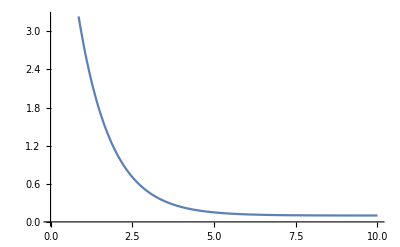

```mathematica
Plot[Exp[-(x-2)]+0.1,{x,0,10}]
```

```mathematica
bumpswitch[cs2nint_,b_,cmax_,ns_,mag_,width_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,dec,B},
(*start with sly, cs2nint,  then Gaussian, then exponential -> cmax*)

(*ns[[1]] ->  start bump
ns[[2]] -> downward after bump
*)
fun[x_]:=cs2nint[ns[[1]]]+mag[[1]]*Exp[-(x-ns[[2]])^2/width^2];
dec[x_]:=cmax+mag[[2]]*Exp[-(x-B)];

B=ns[[2]] -Log[(c1[ns[[2]]]+cmax)/mag[[2]]]  ;
c1[x_]:=s[x,ns[[1]],b]* fun[x]+(1-s[x,ns[[1]],b])*cs2nint[x];
(*c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];*)
c2[x_]:=Which[x<ns[[2]],c1[x],x> ns[[2]],dec[x]];
Return[c2];
]
```

```mathematica
fx[f1_,f2_,ns_]:=Module[{p1,p2,x0,y0,f},
p1={ns[[1]],f1[ns[[1]]]};
p2={ns[[2]],f2[ns[[2]]]};

x0=(p2[[2]]-p1[[2]]+(p1[[1]]^2-p2[[1]]^2))/(2.(p1[[1]]-p2[[1]]));
y0=p2[[2]]-(p2[[1]]-x0)^2;

f[x_]:=(x-x0)^2+y0;
Return[f];
]
```

```mathematica
runosc[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag*Exp[(-b[[2]]*x)/(2width)]Cos[freq*x+off]+cmax;
c1[x_]:=s[x,ns,b[[1]]] osc[x]+(1-s[x,ns,b[[1]]])*cs2nint[x];

Return[c1];
]
```

```mathematica
disbump1[cs2nint_,b_,cmax_,ns_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name},
c1[x_]:=If[x<ns,cs2nint[x], cmax];
Return[c1];
]

disbump2[cs2nint_,ns_,mag_,width_,off_]:=Module[{c2,out,fun,fout},

fun[x_]:=1/3.-mag*Exp[-(x-off)^2/width^2];
fout=fx[cs2nint,fun,ns];
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[2]],fout[x],x> ns[[2]],fun[x]];
Return[c2];
]
```

```mathematica
runoscbump[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag[[2]]*Exp[(-b[[3]]*x)/(2width[[2]])]Cos[freq*x+off[[2]]]+cmax[[2]];
c1[x_]:=s[x,ns[[1]],b[[1]]] (fun[x,mag[[1]],width[[1]],off[[1]]]+cmax[[1]])+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];
c2[x_]:=s[x,ns[[2]],b[[2]]]*osc[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
Return[c2];
]
```

```mathematica
cp1=disbump1[cs2low,0.5,1./3,4]
cp2=disbump2[cs2low,{4,5},-0.3,0.2,6]
cp3=disjump[cs2low,{0.5,0.2},{0.5,0.7},{4,4.2},-0.5,0.1,4.5]
```

c1$302910

c2$302911

c2$302913

```mathematica
cs2EOS[f_,sly_,swt_]:=Module[{in,tabgcm3,ϵofp,pofϵ,out,dpde,plot,eosall,noout,eosmr,eosin,suot},
eosall=comblowden[sly,f,swt];
Print["eos done"];

(*out=Table[{sly[[i,1]],sly[[i,4]]},{i,Length[sly]}];
Print[csplot[out,f]];*)

(*out=Table[{gcm3toMeVfm3*eosall[[i,3]],1.6022*10^33*eosall[[i,2]]},{i,Length[eosall]}];
sout=Table[{gcm3toMeVfm3*sly[[i,3]],1.6022*10^33*sly[[i,2]]},{i,Length[sly]}];
Print[Show[{ListLogLogPlot[{sout,out},PlotRange->{{10^14,10^16},{10^32,10^37}},AspectRatio->0.9,PlotStyle->MyStyle,FrameLabel->{Style["ε [g cm^-3]",15],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[15]],leg2[{"sly","function"},{0,0.10,0.12}+0.7,{0.4,0.3,0.2,0.1}-0.2,MyStyle]}]];*)

eosin=ConvertInterpolate[eosall];
noout=Select[genmr[eosin],#[[2]]<4&];

(*plot=ListLinePlot[noout[[All,1;;2]],PlotStyle->MyStyle,AspectRatio->0.9,PlotStyle->MyStyle,FrameLabel->{Style["R [km]",15],Style["M",20]},ImageSize->500,Frame->True,LabelStyle->Directive[15]];*)

Return[{noout,eosall}];
]
```

```mathematica
mrTWout[f_,sly_,swt_]:=Module[{in,tabgcm3,ϵofp,pofϵ,out,dpde,plot,eosall,noout,eosmr,eosin,suot},
eosall=comblowden[sly,f,swt];

eosin=ConvertInterpolate[eosall];
noout=Select[genmrTW[eosin],#[[2]]<4&];

Return[{noout,eosall}];
]
```

```mathematica
wraper[folder_,funs_]:=Module[{all,mrall,eosall,csplot,suplot,mrplot},
CreateDirectory[StringJoin["output_files/",folder]];
all=Table[cs2EOS[funs[[i]],sly,0.8],{i,Length[funs]}];

Print["here"];
mrall=all[[All,1]];

eosall=all[[All,2]];
csplot=csplotvar[cs2sly,funs];
suplot=stupidunits[sly,eosall];
mrplot=MRmany[mrsly,mrall];
SetDirectory[NotebookDirectory[]];

Export[StringJoin["output_files/",folder,"/cs2plot.png"],csplot];
Export[StringJoin["output_files/",folder,"/stupidunitsplot.png"],suplot];
Export[StringJoin["output_files/",folder,"/mrplot.png"],mrplot];
For[i=1,i≤Length[funs],i++,
Export[StringJoin["output_files/",folder,"/eos",ToString[i],".dat"],eosall[[i]]];
Export[StringJoin["output_files/",folder,"/mr",ToString[i],".dat"],mrall[[i]]];
]
]
```

```mathematica
wraperTW[folder_,funs_]:=Module[{all,mrall,eosall,csplot,suplot,mrplot},
CreateDirectory[StringJoin["output_files/",folder]];
all=Monitor[Table[mrTWout[funs[[i]],sly,0.8],{i,Length[funs]}],i];
Print["here"];
mrall=all[[All,1]];
eosall=all[[All,2]];
csplot=csplotvar[cs2sly,funs];
suplot=stupidunits[sly,eosall];
mrplot=MRmany[mrsly,mrall[[All,All,1;;2]]];
SetDirectory[NotebookDirectory[]];
Print[mrplot];
Export[StringJoin["output_files/",folder,"/cs2plot.png"],csplot];
Export[StringJoin["output_files/",folder,"/stupidunitsplot.png"],suplot];
Export[StringJoin["output_files/",folder,"/mrplot.png"],mrplot];
For[i=1,i≤Length[funs],i++,
Export[StringJoin["output_files/",folder,"/eos",ToString[i],".dat"],eosall[[i]]];
Export[StringJoin["output_files/",folder,"/mr",ToString[i],".dat"],mrall[[i]]];
];

]
```

## Crust [Always run]

### SLY [default]

```mathematica
sly=Import["input_files/sly/eos.dat"];
mrsly=mcut[Import["input_files/sly/mr.dat"]];
cs2sly=Table[{sly[[i,1]],sly[[i,4]]},{i,Length[sly]}];
cs2low=Interpolation[cs2sly,InterpolationOrder->1];
```

## c_s^2 functional forms [run individually ONLY and as needed!]

### width of peak

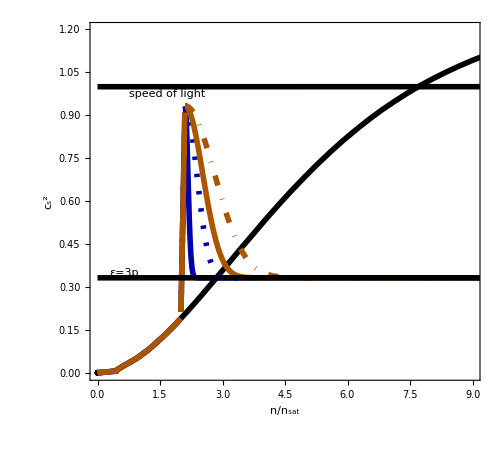

General::munfl: Exp[-710.222] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-715.562] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

Part::partw: Part {1,3,7,8,9,15,20,21,25,26,27,30,31,32,33,34,35,36,38,41,44} of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Rasterize::bigraster: Not enough memory available to rasterize Notebook expression.

```mathematica
f0=disbump2[cs2low,{2.0,2.1},-0.6,0.1,2.1];
f1=disbump2[cs2low,{2.0,2.1},-0.6,0.4,2.1];
f2=disbump2[cs2low,{2.0,2.1},-0.6,0.6,2.1];
f3=disbump2[cs2low,{2.0,2.1},-0.6,1,2.1];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["adjustedwidth",{f0,f1,f2,f3}]
```

### location of peak

```mathematica
f0=disbump2[cs2low,{1.5,1.6},-0.6,1,1.6];
f1=disbump2[cs2low,{2.0,2.1},-0.6,1,2.1];
f2=disbump2[cs2low,{2.4,2.5},-0.6,1,2.5];
f3=disbump2[cs2low,{3.0,3.1},-0.6,1,3.1];
```

```mathematica
wraper["peaklocation",{f0,f1,f2,f3}]
```

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/peaklocation already exists.

General::munfl: -0.6 3.01653×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.624] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.157] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
csplot[cs2low,f0,f1,f2,f3]
stupidunits[sly,{f0eos,f1eos,f2eos,f3eos}]
MRmany[mrsly,{f0mr,f1mr,f2mr,f3mr}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
f0=disbump2[cs2low,{1.95,2.05},-0.65,0.7,2.05];
f1=disbump2[cs2low,{2.0,2.1},-0.6,1,2.1];
f2=disbump2[cs2low,{2.4,2.5},-0.6,2.5,2.5];
f3=runosc[cs2low,{0.2,0.005},3,0.91,0.1,0.5,0.5,0];
csplot[cs2sly,f0,f1,f2,f3]
wraper["peaklocation_adjustwidth",{f0,f1,f2,f3}]
```

-Graphics-

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/peaklocation_adjustwidth already exists.

General::munfl: -0.65 2.40129×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.081] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.842] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

eos done

here

```mathematica
csplot[cs2ex,f0,f1,f2,f3]
stupidunits[sly,{f0eos,f1eos,f2eos,f3eos}]
MRmany[mrsly,{f0mr,f1mr,f2mr,f3mr}]
```

-Graphics-

-Graphics-

-Graphics-

### runbump3

```mathematica
runbump3[cs2nint_,b_,cmax_,ns_,mag_,width_,off_,g_,meq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,ff},

c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
c3[x_]:=s[x,ns[[3]],b[[3]]]*fun[x,mag[[2]],width[[2]],off[[2]]]+(1-s[x,ns[[3]],b[[3]]])*c2[x];

Return[c3];
]
```

```mathematica
mroutsly=runbump3[{0.2,0.2,0.2},{0.9},{3,4,9},{0.1,-0.8},{0.1,0.1},{2,5},1,master];
```

### runoscbump

```mathematica
f1=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.5},{0.1,0.5},{89,0.6},{0.1,0.05},{0.01,0.5},2.5]
cs2EOS[f1,sly,2.5]
```

c2$92289

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

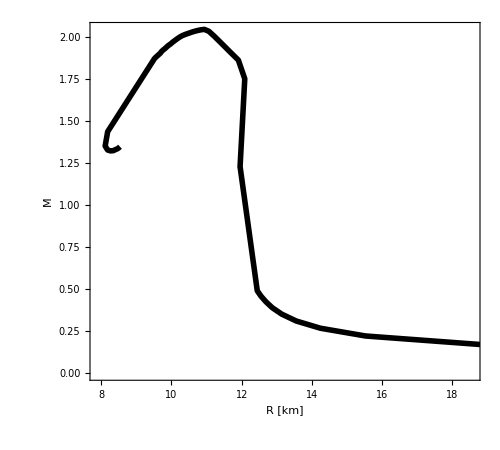
{-Graphics-,{{23.2037,0.115136},{18.8825,0.170535},{15.5263,0.222573},{14.241,0.268786},{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{11.9543,1.23089},{12.0881,1.75379},{11.905,1.8653},{11.6377,1.92038},{11.4097,1.96807},{11.219,2.00735},{11.0654,2.0366},{10.9372,2.04804},{10.84,2.04559},{10.7122,2.03972},{10.5958,2.03273},{10.3919,2.01795},{10.3049,2.01034},{10.2335,2.00189},{10.1656,1.99223},{10.0987,1.98206},{10.0334,1.97176},{9.97736,1.96154},{9.90927,1.95155},{9.85756,1.9419},{9.81145,1.93294},{9.75852,1.9243},{9.71462,1.91556},{9.68493,1.90678},{9.54793,1.88085},{9.51209,1.87273},{9.4886,1.8649},{8.1846,1.43924},{8.1126,1.35374},{8.18251,1.33003},{8.26452,1.32462},{8.35133,1.32629},{8.39212,1.33095},{8.45946,1.33684},{8.50236,1.34314},{8.53526,1.34945}}}

```mathematica
f1=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.5},{0.1,0.5},{89,0.6},{0.1,0.05},{0.01,0.5},2.5]
cs2EOS[f1,sly,2.5]
```

```mathematica
runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.4},{0.1,0.4},{0.08,0.5},3]
(*runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.01},{0.5,0.5},{0.08,0.5},3]
runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.01},{0.5,0.5},{0.08,0.5},3]*)
```

runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.4},{0.1,0.4},{0.08,0.5},3]

Import::nffil: File data/runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.4},{0.1,0.4},{0.08,0.5},3]/MR.dat not found during Import.

```mathematica
runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.01},{0.1,0.4},{0.08,0.5},3]
```

runoscbump[{0.2,0.1,0.005},{2,3},{0.3,0.5},{1,0.01},{0.1,0.4},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.01},{0.5,0.5},{0.08,0.5},3]
runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.01},{0.5,0.5},{0.08,0.5},3]
runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.01},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.01},{0.5,0.5},{0.08,0.5},3]

runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.01},{0.5,0.5},{0.08,0.5},3]

runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.01},{0.5,0.5},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.1},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{4.5,5},{0.6,0.33},{4,0.1},{0.5,0.5},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.1},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{3,4},{0.6,0.33},{3,0.1},{0.5,0.5},{0.08,0.5},3]

```mathematica
runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.1},{0.5,0.5},{0.08,0.5},3]
```

runoscbump[{0.1,0.1,0.005},{2,3},{0.6,0.33},{2,0.1},{0.5,0.5},{0.08,0.5},3]

### oscilllations

```mathematica
runoscbump[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag[[2]]*Exp[(-b[[3]]*x)/(2width[[2]])]Cos[freq*x+off[[2]]]+cmax[[2]];
c1[x_]:=s[x,ns[[1]],b[[1]]] (fun[x,mag[[1]],width[[1]],off[[1]]]+cmax[[1]])+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];
c2[x_]:=s[x,ns[[2]],b[[2]]]*osc[x]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
Return[c2];
]
```

```mathematica
o1=runosc[cs2low,{0.2,0.005},2,0.8,0.1,0.5,0.5,0]
o2=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.5},{0.1,0.5},{89,0.6},{0.1,0.05},{0.01,0.5},2.5]
o3=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,2.1},{0.1,0.5},{89,0.4},{0.1,0.05},{0.01,0.5},2.1]
o4=runoscbump[cs2low,{0.01,0.05,0.005},{2.0,3},{0.5,0.3},{0.7,0.1},{0.1,0.05},{0.01,0.5},3]
wraper["oscilliations",{o1,o2,o3,o4}]
```

c1$363230

c2$363231

c2$363232

c2$363233

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/oscilliations already exists.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

eos done

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

here

```mathematica
csplot[cs2ex,o1,o2,o3,o4]
stupidunits[sly,{o0eos,o1eos,o2eos,o3eos}]
MRmany[mrsly,{o0mr,o1mr,o2mr,o3mr}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Log[10,14.]
```

1.14613

### double small bumps

c2$388731

c2$388732

c2$388733

c2$388734

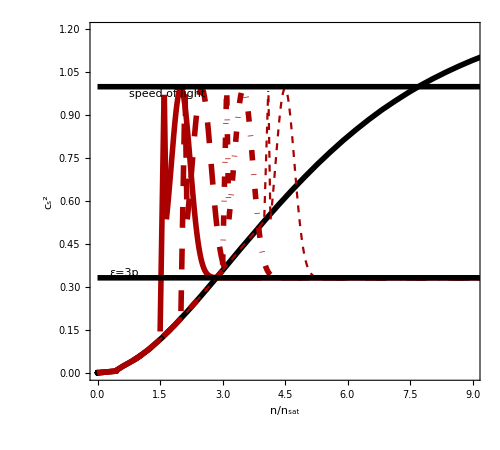

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/2bumpsfat already exists.

General::munfl: Exp[-708.891] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.556] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.223] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
cp0=disjump[cs2low,{0.5,0.2},{0.5,1.0},{1.5,1.65},-0.66,0.32,2]
cp1=disjump[cs2low,{0.5,0.2},{0.5,1.0},{2,2.15},-0.66,0.32,2.5]
cp2=disjump[cs2low,{0.5,0.2},{0.5,1.0},{3,3.15},-0.66,0.32,3.5]
cp3=disjump[cs2low,{0.5,0.2},{0.5,1.0},{4,4.15},-0.66,0.32,4.5]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
wraper["2bumpsfat",{cp0,cp1,cp2,cp3}]
```

c2$414512

c2$414513

c2$414514

c2$414515

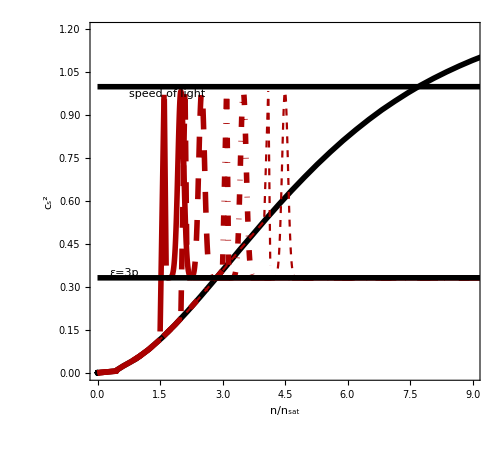

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/2bumpsthin already exists.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
cp0=disjump[cs2low,{0.5,0.2},{0.5,1.0},{1.5,1.65},-0.65,0.1,2]
cp1=disjump[cs2low,{0.5,0.2},{0.5,1.0},{2,2.15},-0.65,0.1,2.5]
cp2=disjump[cs2low,{0.5,0.2},{0.5,1.0},{3,3.15},-0.65,0.1,3.5]
cp3=disjump[cs2low,{0.5,0.2},{0.5,1.0},{4,4.15},-0.65,0.1,4.5]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
wraper["2bumpsthin",{cp0,cp1,cp2,cp3}]
```

```mathematica
cp0=disjump[cs2low,{0.5,0.2},{0.5,1.0},{1.5,1.65},-0.6,0.1,2]
cp1=disjump[cs2low,{0.5,0.2},{0.5,1.0},{2,2.15},-0.6,0.1,2.5]
cp2=disjump[cs2low,{0.5,0.2},{0.5,1.0},{3,3.15},-0.6,0.1,3.5]
cp3=disjump[cs2low,{0.5,0.2},{0.5,1.0},{4,4.15},-0.6,0.1,4.5]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
```

### end point

```mathematica
disbumpend[cs2nint_,ns_,mag_,width_,off_,final_]:=Module[{c2,out,fun,fout},

fun[x_]:=final-mag*Exp[-(x-off)^2/width^2];
fout=fx[cs2nint,fun,ns];
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[2]],fout[x],x> ns[[2]],fun[x]];
Return[c2];
]
```

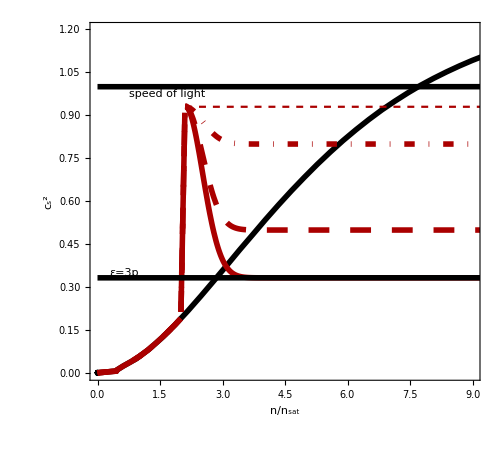

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/endpoint already exists.

General::munfl: Exp[-708.447] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.223] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
f0=disbumpend[cs2low,{2.0,2.1},-0.6,0.6,2.1,1/3.];
f1=disbumpend[cs2low,{2.0,2.1},-0.43,0.6,2.1,0.5];
f2=disbumpend[cs2low,{2.0,2.1},-0.13,0.6,2.1,0.8];
f3=disbumpend[cs2low,{2.0,2.1},0,0.6,2.1,0.93];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["endpoint",{f0,f1,f2,f3}]
```

```mathematica
disbumpend[cs2nint_,ns_,mag_,width_,off_,final_]:=Module[{c2,out,fun,fout},

fun[x_]:=final-mag*Exp[-(x-off)^2/width^2];
fout=fx[cs2nint,fun,ns];
c2[x_]:=Which[x<ns[[1]],cs2nint[x],ns[[1]]≤ x≤ ns[[2]],fout[x],x> ns[[2]],fun[x]];
Return[c2];
]
```

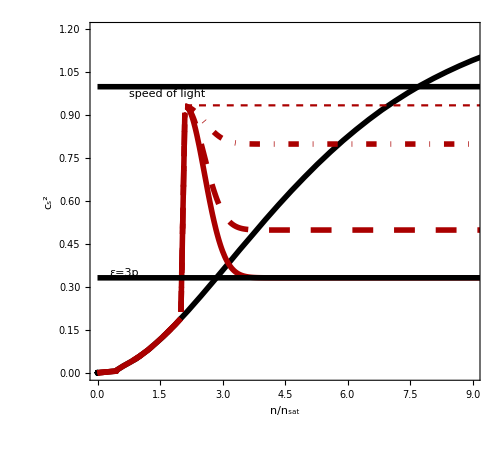

```mathematica
f0=disbumpend[cs2low,{2.0,2.1},-0.6,0.66,2.1,1/3.];
f1=disbumpend[cs2low,{2.0,2.1},-0.43,0.65,2.1,0.5];
f2=disbumpend[cs2low,{2.0,2.1},-0.13,0.65,2.1,0.8];
f3=disbumpend[cs2low,{2.0,2.1},0,0.6,2.1,0.935];
csplotvar[cs2low,{f0,f1,f2,f3}]
(*wraper["endpoint2",{f0,f1,f2,f3}]*)
```

```mathematica
`
```

```mathematica
0.1/2.8*100
```

3.57143

```mathematica
(16-15.5)/16*100
```

3.125

```mathematica
0.1/1.1*100
```

9.09091

```mathematica
(11.81958427590623-11.549349555966765)/11.549349555966765*100
```

2.33983

3.5 % change in n/sat -> 2 % change in R (high n/nsat)
9 % change in n/nsat -> 3 % change in R (low n/nsat)

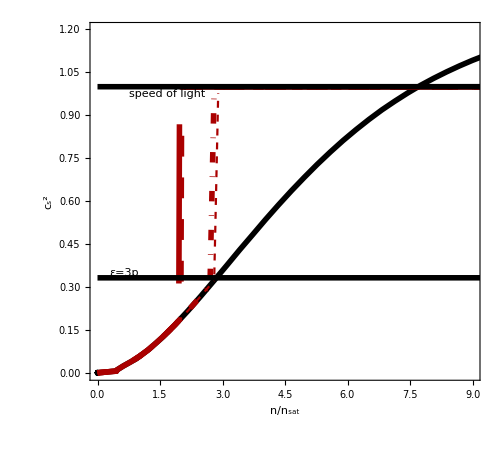

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/endpoint_max already exists.

General::munfl: Exp[-708.447] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.223] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
f0=disbumpend[cs2low,{1.95,1.97},0,0.6,1.95,0.999];
f1=disbumpend[cs2low,{2.0,2.02},0,0.6,2.0,0.999];
f2=disbumpend[cs2low,{2.7,2.8},0,0.6,2.1,0.999];
f3=disbumpend[cs2low,{2.8,2.9},0,0.6,2.1,0.999];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["endpoint_max",{f0,f1,f2,f3}]
```

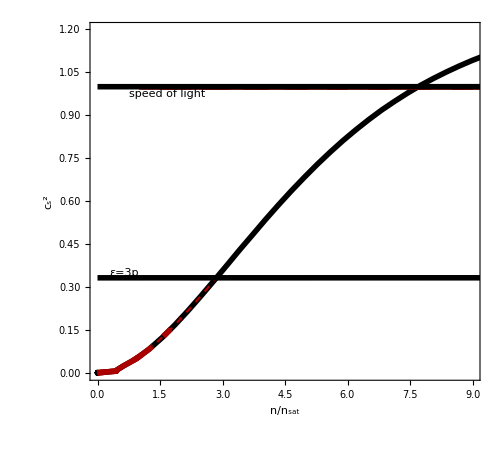

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/endpoint_noslant already exists.

General::munfl: Exp[-708.447] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.222] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
f0=disbumpend[cs2low,{1.0,1.001},0,0.6,1.1,0.999];
f1=disbumpend[cs2low,{1.5,1.501},0,0.6,2.1,0.999];
f2=disbumpend[cs2low,{2.0,2.001},0,0.6,2.1,0.999];
f3=disbumpend[cs2low,{3.0,3.001},0,0.6,2.1,0.999];
csplotvar[cs2sly,{f0,f1,f2,f3}]
wraper["endpoint_noslant",{f0,f1,f2,f3}]
```

```mathematica
ffas[x_]:=1/x
Integrate[ffas[x],x]
```

Log[x]

### slanted

```mathematica
runosc[cs2nint_,b_,ns_,cmax_,mag_,width_,off_,freq_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name,osc},
osc[x_]:=mag*Exp[(-b[[2]]*x)/(2width)]Cos[freq*x+off]+cmax;
c1[x_]:=s[x,ns,b[[1]]] osc[x]+(1-s[x,ns,b[[1]]])*cs2nint[x];

Return[c1];
]
```

c1$517940

c1$517941

c1$517942

c1$517943

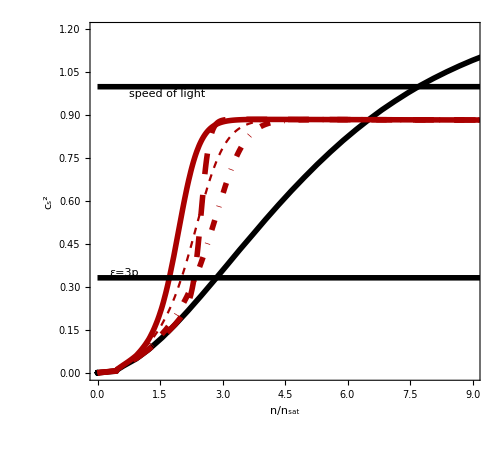

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/slanted already exists.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

```mathematica
cp0=runosc[cs2low,{0.5,0.005},2,0.8,0.1,0.5,0.5,0]
cp1=runosc[cs2low,{0.2,0.005},2.5,0.8,0.1,0.5,0.5,0]
cp2=runosc[cs2low,{0.7,0.005},3,0.8,0.1,0.5,0.5,0]
cp3=runosc[cs2low,{0.7,0.005},2.5,0.8,0.1,0.7,0.5,0]
csplotvar[cs2low,{cp0,cp1,cp2,cp3}]
wraper["slanted",{cp0,cp1,cp2,cp3}]
```

### Bigbump

c1$215480

c1$215481

c1$215482

c1$215483

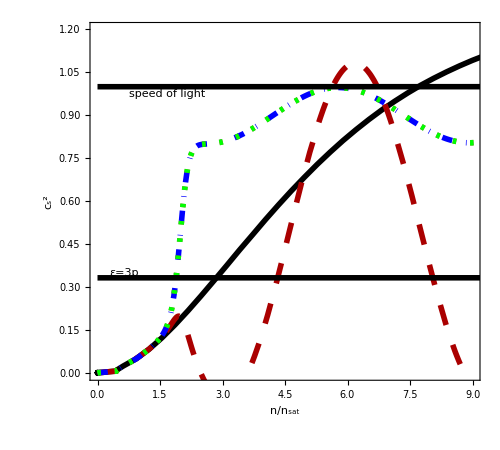

```mathematica
cp0=runosc[cs2low,{0.2,0.005},2,0.5,0.6,0.5,0.1,1]
cp1=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,1]
cp2=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,1]
cp3=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,1]
csplotvar[cs2ex,{cp0,cp1,cp2,cp3}]
(*wraper["2bumpsfat",{cp0,cp1,cp2,cp3}]*)
```

### After Bump

```mathematica
runbump2[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
c3[x_]:=s[x,ns[[3]],b[[3]]]*fun[x,mag[[2]],width[[2]],off[[2]]]+(1-s[x,ns[[3]],b[[3]]])*c2[x];

Return[c3];
]
```

```mathematica
eosall=comblowden[sly,crz0,0.8];
eosin=ConvertInterpolate[eosall];
```

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.111] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

c3$584900

c3$584901

c3$584902

c3$584903

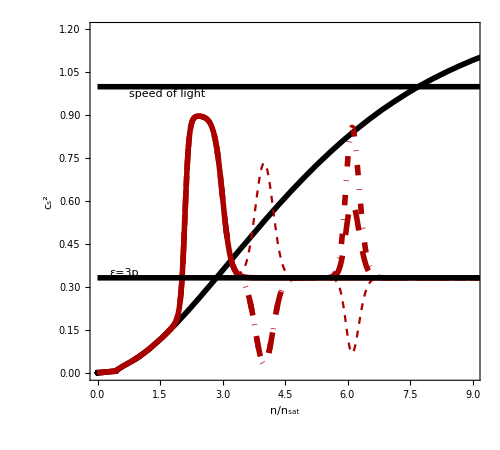

```mathematica
crz0=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,7},{0,0},{0.3,0.3},{5,7}]
crz1=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,6},{0.3,-0.4},{0.3,0.3},{4,6}]
crz2=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,6},{0.3,-0.8},{0.3,0.3},{4,6}]
crz3=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2.1,3,6},{-0.4,0.4},{0.3,0.3},{4,6}]
csplotvar[cs2low,{crz0,crz1,crz2,crz3}]
```

```mathematica
wraper["afterbump",{crz0,crz1,crz2,crz3}]
```

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/afterbump already exists.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.111] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

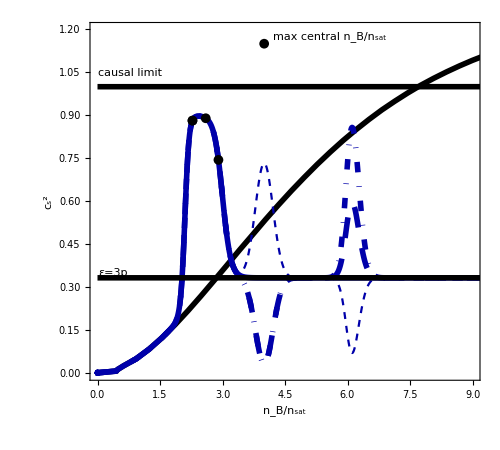
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
miniplots[10]
```

### Boring

```mathematica
runbump2[cs2nint_,b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];

Return[c2];
]
```

c3$845753

c3$845754

c3$845755

c3$845756

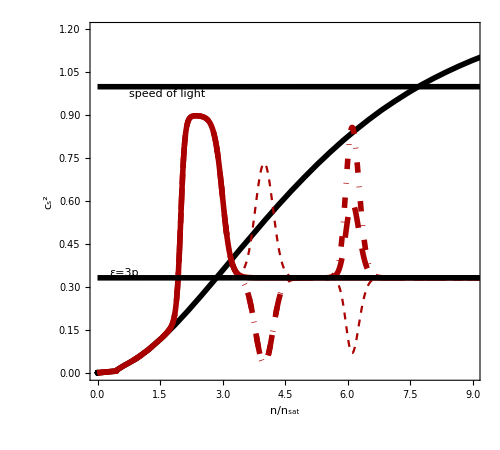

```mathematica
crz0=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,7},{0,0},{0.3,0.3},{5,7}]
crz1=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,6},{0.3,-0.4},{0.3,0.3},{4,6}]
crz2=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,6},{0.3,-0.8},{0.3,0.3},{4,6}]
crz3=runbump2[cs2low,{0.1,0.2,0.2},{0.9,1./3,1./3},{2,3,6},{-0.4,0.4},{0.3,0.3},{4,6}]
csplotvar[cs2ex,{crz0,crz1,crz2,crz3}]
```

```mathematica
wraper["afterbump",{crz0,crz1,crz2,crz3}]
```

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/afterbump already exists.

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: Exp[-709.334] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-711.111] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

here

### runosc

```mathematica
cp=runosc[cs2low,{0.2,0.005},4,0.5,0.1,0.5,0.5,3]
cp1=disbump1[cs2low,0.5,1./3,4]
cp2=disbump2[cs2low,{0.5,0.2},{0.5,0.1},{4,5},-0.3,0.2,6]
cp3=disjump[cs2low,{0.5,0.2},{0.5,0.7},{4,4.2},-0.5,0.1,4.5]
```

c1$80212

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

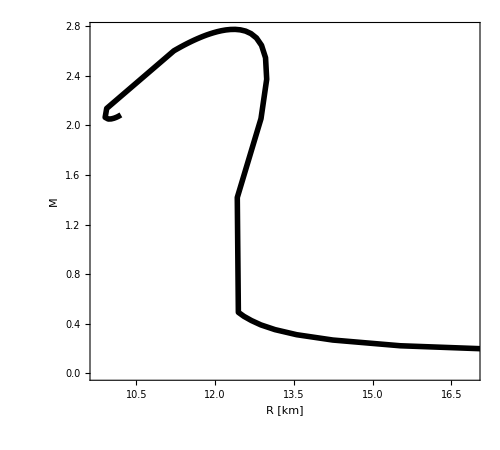
{-Graphics-,{{23.2037,0.115136},{18.8825,0.170535},{15.5263,0.222573},{14.241,0.268786},{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{12.423,1.41807},{12.8744,2.05394},{12.9829,2.37146},{12.9609,2.5446},{12.8847,2.64464},{12.7881,2.70407},{12.6839,2.73933},{12.5815,2.75945},{12.4802,2.76973},{12.3844,2.77343},{12.2925,2.77265},{12.2041,2.76877},{12.1226,2.76273},{12.0443,2.7552},{11.9713,2.74662},{11.9015,2.73733},{11.8345,2.72758},{11.7723,2.71754},{11.7133,2.70734},{11.6568,2.69708},{11.6031,2.68683},{11.5518,2.67664},{11.5031,2.66656},{11.4565,2.65661},{11.4119,2.64681},{11.3693,2.63719},{11.3288,2.62774},{11.2897,2.61848},{11.2517,2.60941},{11.2158,2.60054},{9.93713,2.1361},{9.9078,2.06409},{9.96716,2.0506},{10.0237,2.0516},{10.0751,2.0571},{10.1178,2.06393},{10.1532,2.07093},{10.1814,2.07764},{10.2075,2.08391}}}

```mathematica
cp=runosc[cs2low,{0.2,0.005},2,0.8,0.1,0.5,0.5,0]
cs2EOS[cp,sly,2]
```

c1$77469

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

-Graphics-

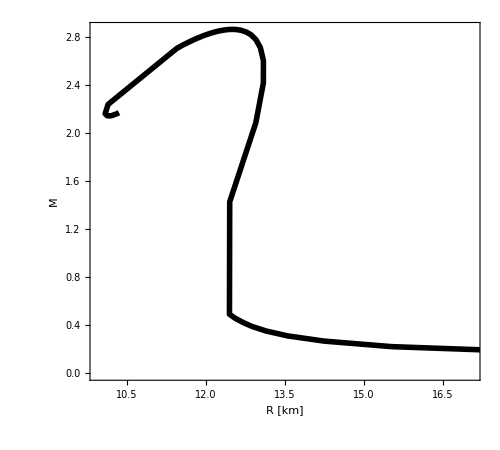
{-Graphics-,{{23.2037,0.115136},{18.8825,0.170535},{15.5263,0.222573},{14.241,0.268786},{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{12.4484,1.42879},{12.9438,2.0853},{13.0883,2.41877},{13.0888,2.60353},{13.0312,2.71219},{12.948,2.77819},{12.8567,2.81858},{12.7614,2.84281},{12.668,2.85643},{12.5773,2.86291},{12.4906,2.86444},{12.4081,2.86253},{12.329,2.85817},{12.2544,2.85208},{12.1826,2.84475},{12.1163,2.83656},{12.0521,2.82777},{11.9914,2.81858},{11.9335,2.80913},{11.8807,2.79954},{11.8261,2.78989},{11.7758,2.78024},{11.7281,2.77063},{11.6818,2.76111},{11.639,2.7517},{11.5967,2.74243},{11.5537,2.7333},{11.5177,2.72432},{11.4813,2.71551},{11.4456,2.70687},{10.1361,2.23939},{10.0811,2.16223},{10.119,2.1455},{10.1759,2.14425},{10.2209,2.1481},{10.2506,2.15368},{10.2917,2.15971},{10.3198,2.16566},{10.3436,2.1713}}}

```mathematica
cp=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,0]
cs2EOS[cp,sly,2]
```

c1$74726

InterpolatingFunction::dmval: Input value {9.62} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.63} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.64} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

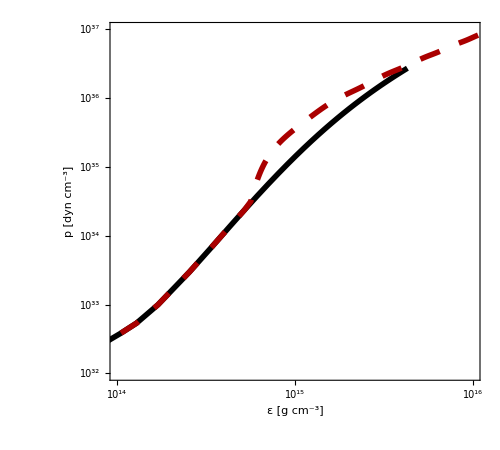

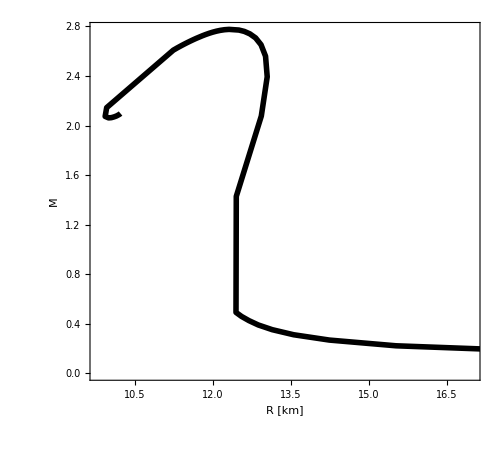
{-Graphics-,{{23.2037,0.115136},{18.8825,0.170535},{15.5263,0.222573},{14.241,0.268786},{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{12.4492,1.42857},{12.931,2.07691},{13.0447,2.39374},{13.0126,2.55972},{12.9256,2.65254},{12.8215,2.7072},{12.7104,2.7402},{12.6039,2.75989},{12.5,2.77083},{12.3101,2.77627},{12.2234,2.77359},{12.1418,2.7685},{12.0653,2.76162},{11.9925,2.75346},{11.924,2.74439},{11.8587,2.73474},{11.7965,2.72473},{11.6804,2.70426},{11.6265,2.69402},{11.5748,2.68386},{11.5256,2.67383},{11.4784,2.66396},{11.4335,2.65426},{11.3906,2.64476},{11.3496,2.63547},{11.3099,2.62637},{11.2736,2.61747},{11.2371,2.60876},{9.95326,2.14473},{9.92387,2.07387},{9.98997,2.06198},{10.0447,2.06399},{10.0963,2.07008},{10.1418,2.07726},{10.1739,2.08444},{10.2023,2.09124},{10.2197,2.09753}}}

```mathematica
cp=runosc[cs2low,{0.2,0.005},2,0.9,0.1,0.5,0.5,3]
cs2EOS[cp,sly,2]
```

```mathematica
cp=runosc[cs2low,{0.2,0.005},4,0.33,0.1,0.5,0.5,3]
cp1=disbump1[cs2low,0.5,1./3,4]
cp2=disbump2[cs2low,{0.5,0.2},{0.5,0.1},{4,5},-0.3,0.2,6]
cp3=disjump[cs2low,{0.5,0.2},{0.5,0.7},{4,4.2},-0.5,0.1,4.5]
csplot[cs2ex,cp3]
eosout=comblowden[tabMeVfm3,cp3,4]
(*mrout=genmr[eosout]
ListLinePlot[mrout]*)
```

c1$5176

c1$5177

{4,0.531019}

{5,0.333333}

{4.59884,0.172406}

c2$5178

c2$5180

-Graphics-

General::munfl: Exp[-712.89] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-718.24] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-723.61] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{InterpolatingFunction[…],21[…],{1},{{2.14432×10^-6,41.5964},{0.0000136728,131.539},{0.000087182,415.964},{0.000555899,1315.39},{0.00354458,4159.65},{0.0226013,13154.},1667,{3.17202×10^15,9.80841×10^15},{3.17419×10^15,9.81491×10^15},{3.17635×10^15,9.82142×10^15},{3.17852×10^15,9.82793×10^15},{3.18069×10^15,9.83444×10^15},{3.18286×10^15,9.84095×10^15}}}
 |  |  |  |

```mathematica
cso[list_]:=Delete[Table[{list[[i,1]]/nsat,list[[i,4]]},{i,Length[list]}],1]
```

```mathematica
(*runbump3[b_,cmax_,ns_,mag_,width_,off_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,name},
c1[x_]:=s[x,ns[[1]],b[[1]]] cmax[[1]]+(1-s[x,ns[[1]],b[[1]]])*cs2nint[x];

c2[x_]:=s[x,ns[[2]],b[[2]]]*fun[x,mag[[1]],width[[1]],off[[1]]]+(1-s[x,ns[[2]],b[[2]]])*c1[x];
c3[x_]:=s[x,ns[[3]],b[[3]]]*fun[x,mag[[2]],width[[2]],off[[2]]]+(1-s[x,ns[[3]],b[[3]]])*c2[x];*)
```

```mathematica
runbump1[0.5,1./3,4]
```

InterpolatingFunction::dmval: Input value {9.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.07} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

DeleteFile::fdnfnd: Directory or file /Users/jacquelynnoronhahostler/Dropbox/neutronStars/data/1bump_b0.5_csfin0.333_switch4/eos.dat not found.

```mathematica
runbump2[{0.5,0.2},{0.5,1./3},{4,6},-0.3,0.2,6]
```

General::munfl: Exp[-899.939] is too small to represent as a normalized machine number; precision may be lost.

-Graphics-

InterpolatingFunction::dmval: Input value {9.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.07} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {9.08} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: -0.3 5.13566×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.222] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

DeleteFile::fdnfnd: Directory or file /Users/jacquelynnoronhahostler/Dropbox/neutronStars/data/2bump_b0.5_0.2_csfin0.5_0.333_switch4_6_mag-0.3_width0.2_width6/eos.dat not found.

### playing with interpolation function

28.0771-16.698 x+3.31267 x^2-0.21646 x^3

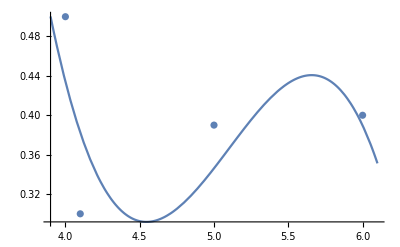

```mathematica
para=Fit[{{4,0.5},{4.1,0.3},{5,0.39},{5.5,0.395},{6,0.4}},{1,x,x^2,x^3},x]
Show[{Plot[para,{x,3.9,6.1}],ListPlot[{{4,0.5},{4.1,0.3},{5,0.39},{6,0.4}}]}]
```

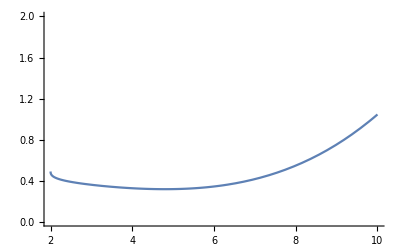

```mathematica
f3[x_,a1_,n1_,a2_,n2_]:=0.5-0.2((x-2)/a1)^n1+0.3((x-3)/a2)^n2
Plot[f3[x,3,1/3,5,3],{x,0,10},PlotRange->{All,{0,2}}]
```

```mathematica
fde[x_]:=0.5-c1((x-b1)/a1)^n1+c2((x-b2)/a2)^n2
```

```mathematica
D[0.5-c1((x-b1)/a1)^n1+c2((x-b2)/a2)^n2,x]
```

```mathematica
Solve[0==-(c1 n1 ((-b1+x)/a1)^(-1+n1))/a1+(c2 n2 ((-b2+x)/a2)^(-1+n2))/a2,x]
```

$Aborted

```mathematica
Solve[A*(-b1+x)^-2==(-b2+x)^-3,x]
```

{{x→-(-1-3 A b2)/(3 A)-(2^(1/3) (-1+6 A b1-6 A b2))/(3 A (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))+((2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))/(3 2^(1/3) A)},{x→-(-1-3 A b2)/(3 A)+((1+ⅈ √3) (-1+6 A b1-6 A b2))/(3 2^(2/3) A (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))-((1-ⅈ √3) (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))/(6 2^(1/3) A)},{x→-(-1-3 A b2)/(3 A)+((1-ⅈ √3) (-1+6 A b1-6 A b2))/(3 2^(2/3) A (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))-((1+ⅈ √3) (2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2+√(4 (-1+6 A b1-6 A b2)^3+(2-18 A b1+27 A^2 b1^2+18 A b2-54 A^2 b1 b2+27 A^2 b2^2)^2))^(1/3))/(6 2^(1/3) A)}}

### flat peak

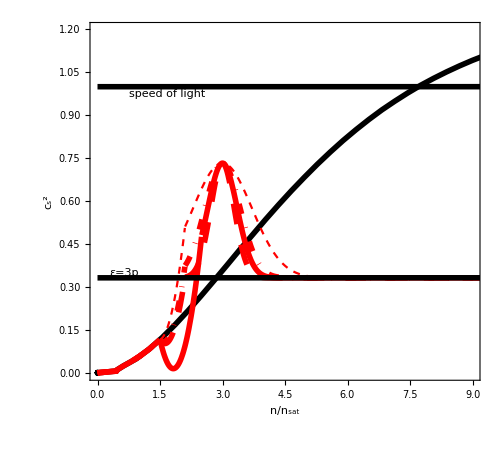

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/flatpeak already exists.

General::munfl: -0.4 5.13566×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-708.624] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.69] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
f0=disbump2[cs2low,{1.5,2.5},-0.4,0.5,3];
f1=disbump2[cs2low,{1.5,2.1},-0.4,0.4,3];
f2=disbump2[cs2low,{1.5,2.1},-0.4,0.6,3];
f3=disbump2[cs2low,{1.5,2.1},-0.4,1,3];
csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["flatpeak",{f0,f1,f2,f3}]
```

```mathematica
bumpswitch[cs2nint_,b_,cmax_,ns_,mag_,width_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,dec,B},
(*start with sly, cs2nint,  then Gaussian, then exponential -> cmax*)

(*ns[[1]] ->  start bump
ns[[2]] -> downward after bump
*)
fun[x_]:=cs2nint[ns[[1]]]+mag*Exp[-(x-ns[[2]])^2/width^2];
B=ns[[2]] +Log[(c1[ns[[2]]]-cmax) ]  ;
dec[x_]:=cmax+Exp[-(x-B)];


c1[x_]:=s[x,ns[[1]],b]* fun[x]+(1-s[x,ns[[1]],b])*cs2nint[x];
c2[x_]:=Which[x<=ns[[2]],c1[x],x> ns[[2]],dec[x]];
Return[c2];
]
bumpswitch2[cs2nint_,b_,cmax_,ns_,mag_,width_]:=Module[{c1,c2,c3,out,mr1,mr2,mr3,plot,fun,name,dec,B,dec2,B2,fun2,call},
(*start with sly, cs2nint,  then Gaussian, then exponential -> cmax*)

(*ns[[1]] ->  start bump
ns[[2]] -> downward after bump
*)
fun[x_]:=cs2nint[ns[[1]]]+mag[[1]]*Exp[-(x-ns[[2]])^2/width[[1]]^2];
B=ns[[2]] +Log[(c1[ns[[2]]]-cmax[[1]])]  ;
dec[x_]:=cmax[[1]]+Exp[-(x-B)];

fun2[x_]:=dec[ns[[3]]]+mag[[2]]*Exp[-(x-ns[[4]])^2/width[[2]]^2];
B2=ns[[4]] +Log[(c2[ns[[4]]]-cmax[[2]])]  ;
dec2[x_]:=cmax[[2]]+Exp[-(x-B2)];


c1[x_]:=s[x,ns[[1]],b]* fun[x]+(1-s[x,ns[[1]],b])*cs2nint[x];
c2[x_]:=s[x,ns[[3]],b]*fun2[x]+(1-s[x,ns[[3]],b])*dec[x];
call[x_]:=Which[x<=ns[[2]],c1[x], ns[[2]]<x<= ns[[3]],dec[x],ns[[3]]<x≤ns[[4]],c2[x],ns[[4]]<x,dec2[x]];
Return[call];
]
```

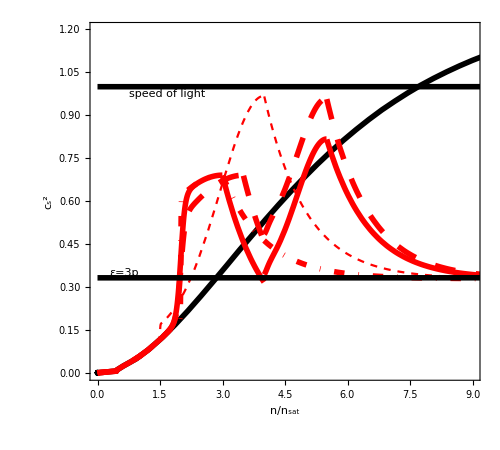

CreateDirectory::filex: /Users/jacquelynnoronhahostler/Dropbox/neutronStars/TOV_public/flatpeak already exists.

eos done

eos done

eos done

«1 more identical outputs»

here

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*bumpswitch[cs2nint_,b_,cmax_,ns_,mag_,width_]*)
f0=bumpswitch2[cs2low,0.1,{0.1,0.33},{2,3,4,5.5},{0.5,0.5},{2.5,1}];
f1=bumpswitch2[cs2low,0.1,{0.1,0.33},{2,3.5,4,5.5},{0.5,0.5},{2.5,1}];
f2=bumpswitch[cs2low,0.01,0.33,{2,3},0.5,2.5];

f3=bumpswitch[cs2low,0.01,0.33,{1.5,4},0.85,1.5]; (*ok*)

csplotvar[cs2low,{f0,f1,f2,f3}]
wraper["flatpeak",{f0,f1,f2,f3}]
```

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

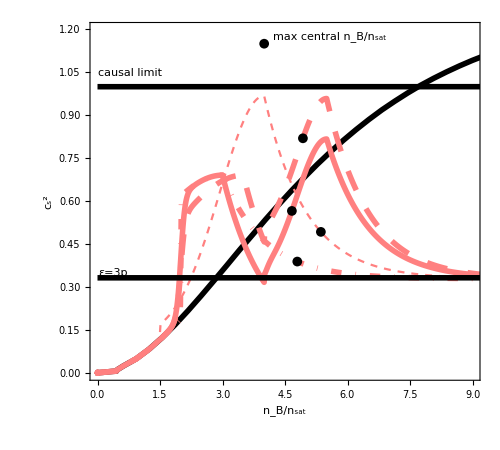
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
miniplots[12]
```

## Summary plots [only run after functional forms are generated]

### normal

```mathematica
mrsum=Show[{MRmany[mrsly,Mfin],txt["(c)",0.3,0.1]}]
(*Export["MRsummary.pdf",mrsum]*)
```

-Graphics-

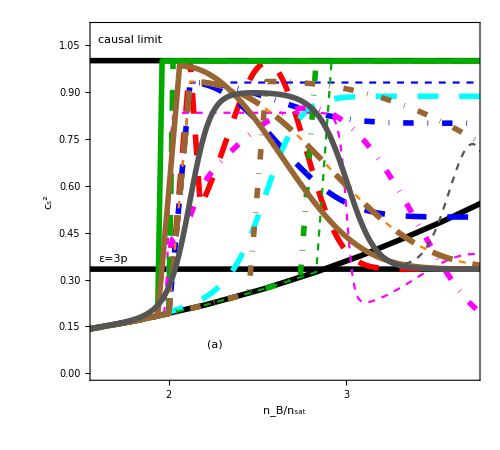

```mathematica
csout=Show[{csplottab[Join[{cs2sly},cssum]],txt["(a)",0.3,0.1]}]
(*Export["cs2summary.pdf",csout]*)
```

```mathematica
eossum=Show[{stupidunits[sly,eosfin],txt["(b)",0.3,0.1]}]
(*Export["EOSsummary.pdf",eossum]*)
```

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

fname = {"2bumpsfat", "endpoint", "peaklocation_adjustwidth", "2bumpsthin", "slanted", "oscilliations", "adjustedwidth", "peaklocation",”afterbump”,”endpoint2”};

```mathematica
miniplots[n_]:=Module[{out,sout,plots,len,sub,eosin,mrin,all,eosall,mrall,mout,lines,psly,p1,p2,p3,dat,fin,str,klist,nBlist,endpoints,mark},
Clear[all];
all=readin[fname[[n]] ];
fin=4*n;
str=fin-3;
klist={1,str+1,str+2,str+3,fin+1};


eosall=all[[1]];
mrall=all[[2]];
mout=Table[mcut[mrall[[i]]][[All,1;;2]],{i,Length[mrall]}];

len=Length[eosall];

nBlist=Table[nBmax[mrall[[j]],eosall[[j]]]/nsat,{j,len}];




sub[eossub_]:=Table[{gcm3toMeVfm3*eossub[[i,3]],1.6022*10^33*eossub[[i,2]]},{i,Length[eossub]}];
out=Table[sub[eosall[[j]]],{j,len}];

sout=Table[{gcm3toMeVfm3*sly[[i,3]],1.6022*10^33*sly[[i,2]]},{i,Length[sly]}];

p1=Show[{ListLogLogPlot[Join[{sout},out],PlotRange->{{10^14,2.5*10^15},{10^32,10^37}},AspectRatio->0.9,PlotStyle->MyStyle[[klist]],FrameLabel->{Style["ε [g cm^-3]",20],Style["p [dyn cm^-3]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]],LIGO[],leg2[{"SLy","LIGO band","f2","f3","f4"},{0,0.10,0.12}+0.5,{0.2,0.1},MyStyle[[{1,2}]]]}];

mrall=Join[{mrsly},mout];
lines=Plot[{2.5+0.00001x,2.67+0.00001x},{x,0,30},PlotStyle->MyStyle[[{1,1,2,3,4,5,6}]],Filling->{1->{2}}];
p2=Show[{ListPlot[mrall,AspectRatio->0.9,PlotRange->{{8.5,17},{0,4}},PlotStyle->MyStyle[[klist]],FrameLabel->{Style["R [km]",20],Style["M [M_⊙]",20]},ImageSize->500,Frame->True,Joined->True,LabelStyle->Directive[20]],ListLinePlot[sly,PlotStyle->MyStyle[[1]]],lines,txt["GW190814",0.05,0.7],txt["GW170817",0.05,0.25],txt["J0030+0451",0.6,0.3],RegionPlot[MRadMin<m<MRadMax&&RadMin<r<RadMax,{r,0,15},{m,0,2}],RegionPlot[GW17m1[[1]]<m<GW17m1[[2]]&&GW17R1[[1]]<r<GW17R1[[2]],{r,0,15},{m,0,2},PlotStyle->Directive[Red,Opacity[0.3]]],RegionPlot[GW17m2[[1]]<m<GW17m2[[2]]&&GW17R2[[1]]<r<GW17R2[[2]],{r,0,15},{m,0,2},PlotStyle->Directive[Red,Opacity[0.3]]],leg2[{"SLy","f1","f2","f3","f4"},{0,0.10,0.12}+0.05,{0.5,1.4,0.3,0.2,0.1}+0.4,MyStyle[[klist]]],txt["(b)",0.8,0.1]}];

dat=Join[{cs2sly},csprint[eosall]];

endpoints=cspoint[dat,nBlist];

psly=ListLinePlot[dat,PlotRange->{{0,9},{0,1.2}},AspectRatio->0.9,PlotStyle->MyStyle[[klist]],FrameLabel->{Style["n_B/n_sat",20],Style["c_s^2",20]},ImageSize->500,Frame->True,LabelStyle->Directive[20]];
lines=Plot[{1/3+0.00001x,1+0.00001x},{x,0,10},PlotStyle->MyStyle[[{1,1}]]];
mark=ListPlot[Join[endpoints,{{4,1.15}}],PlotMarkers->{Automatic,Medium},PlotStyle->MyStyle[[1]]];
p3=Show[Flatten[{psly,lines,txt["ε=3p",0.02,0.3],txt["causal limit",0.02,0.86],mark,txt["max central n_B/n_sat",0.47,0.96],txt["(a)",0.8,0.1]}]];


Export[StringJoin["GW/",fname[[n]],"_stupidunitsplot.pdf"],p1];
Export[StringJoin["GW/",fname[[n]],"_mrplot.pdf"],p2];
Export[StringJoin["GW/",fname[[n]],"_cs2plot.pdf"],p3];


Return[{p1,p2,p3}];
]
```

```mathematica
pMmax[mr_]:=pcen[[ Length[mr]]];
nBfind[eossub_]:=Interpolation[Table[{eossub[[i,2]],eossub[[i,1]]},{i,Length[eossub]}]];
nBmax[mr_,eos_]:=Module[{pM,fun,mc},
mc=mcut[mr];
pM=mc[[ Length[mc],4]];
fun=nBfind[eos];
Return[fun[pM]];
]
cout[cstab_,nb_]:=Module[{int},
int=Interpolation[cstab,InterpolationOrder->1];
Return[{nb,int[nb]}];
]
cspoint[dat_,nblist_]:=Module[{tab,out},
tab=Delete[dat,1];

out=Table[cout[tab[[i]],nblist[[i]]],{i,Length[nblist]}];
Return[out];
]
```

```mathematica
fname
```

{2bumpsfat,endpoint,2bumpsthin,slanted,oscilliations,adjustedwidth,peaklocation,endpoint_max,peaklocation_adjustwidth,afterbump}

```mathematica
{"2bumpsfat","endpoint","2bumpsthin","slanted","oscilliations","adjustedwidth","peaklocation","endpoint_max","peaklocation_adjustwidth","afterbump","endpoint_noslant","endpoint2"}
```

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

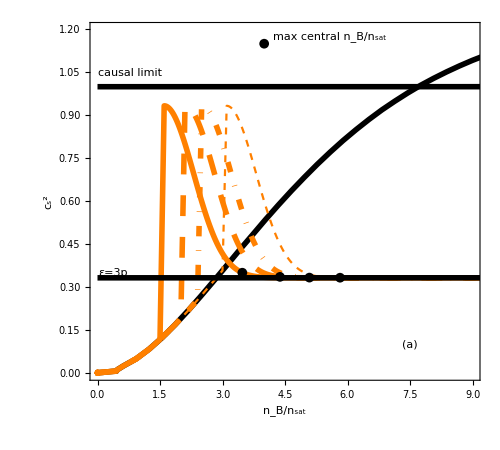
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
miniplots[7]
```

```mathematica
For[i=1,i≤10,i++,
miniplots[i];
]
```

InterpolatingFunction::dmval: Input value {1.00007×10^14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::partw: Part 2 of {} does not exist.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::span: 1;;{}⟦1,1⟧ is not a valid Span specification. A Span specification should be 1, 2, or 3 machine-sized integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

General::stop: Further output of Part::span will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

Interpolation::indat: Data point {{1.4008551221116095,,0.128} contains abscissa {1.4008551221116095,, which is not a real number.

General::stop: Further output of Interpolation::indat will be suppressed during this calculation.

ListPlot::lpn: {{{13.5538,0.311731},{13.141,0.352659},{12.8723,0.390733},{12.6921,0.425891},{12.5501,0.459622},{12.4436,0.492085},{11.8973,1.19029},«6»,{10.6699,2.00201},{10.5555,2.01886},{10.4519,2.03086},{10.356,2.03928},{10.1869,2.04868},{10.11,2.05075},{10.0387,2.05157}},{},{},{},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….